```mathematica
SetDirectory["C:/Users/user/Desktop/Coding/ant/data/sleap"]
```

C:\Users\user\Desktop\Coding\ant\data\sleap

```mathematica
file=Import["n60b18x18VR2019102814cropped.hdf5","Data"];
```

```mathematica
asdf=file⟦"/trajectory_0"⟧;
```

```mathematica
list={};
Do[
asdf=file⟦n⟧;
head=asdf⟦;;,1⟧;
thorax=asdf⟦;;,2⟧;
abdomen=asdf⟦;;,3⟧;
Do[
If[head⟦1,n⟧>1,
(*skip*),
head⟦1,n⟧=head⟦1,n-1⟧;
];
If[head⟦2,n⟧>1,
(*skip*),
head⟦2,n⟧=head⟦2,n-1⟧
]
,{n,1,Length[head⟦1⟧]}];
Do[
If[thorax⟦1,n⟧>1,
(*skip*),
thorax⟦1,n⟧=thorax⟦1,n-1⟧;
];
If[thorax⟦2,n⟧>1,
(*skip*),
thorax⟦2,n⟧=thorax⟦2,n-1⟧
]
,{n,1,Length[thorax⟦1⟧]}];
Do[
If[abdomen⟦1,n⟧>1,
(*skip*),
abdomen⟦1,n⟧=abdomen⟦1,n-1⟧;
];
If[abdomen⟦2,n⟧>1,
(*skip*),
abdomen⟦2,n⟧=abdomen⟦2,n-1⟧
]
,{n,1,Length[abdomen⟦1⟧]}];
avg=(head+thorax+abdomen)/3.;
AppendTo[list,avgᵀ];
,{n,2,Length[file]}]
```

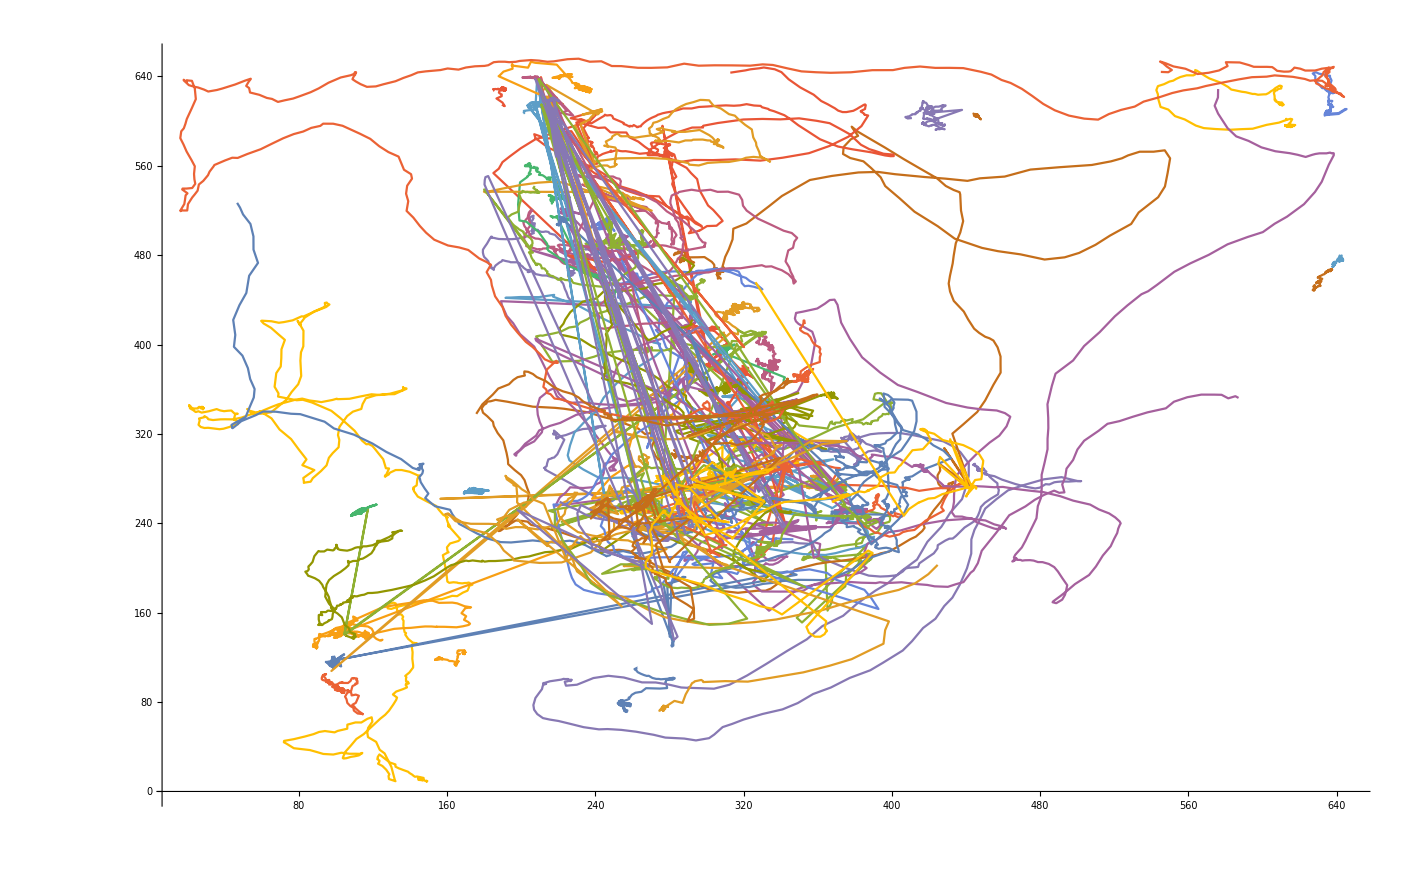

```mathematica
ListPlot[list⟦;;⟧,PlotRange->All,Joined->True]
```

```mathematica
Length@list⟦1⟧
```

500

```mathematica
thorax⟦1,100⟧>0.0001
```

False

```mathematica
thorax
```

{{292.063,292.105,292.121,293.908,293.99,295.879,295.925,295.956,295.972,297.823,297.842,297.972,299.906,299.958,301.961,302.072,302.042,303.821,303.961,305.833,305.802,306.687,306.728,306.761,307.733,308.777,309.712,309.763,309.795,310.667,310.664,310.726,310.731,310.729,310.738,310.713,310.721,310.766,310.771,310.785,312.516,312.567,312.578,312.6,312.662,313.729,311.785,312.697,312.751,313.695,313.73,313.753,313.875,313.696,312.813,310.773,309.811,309.798,310.662,310.747,311.789,314.595,312.755,311.875,335.548,332.457,332.445,325.618,303.884,302.808,302.771,300.782,302.82,302.864,298.823,298.663,293.829,293.829,293.829,293.829,293.829,330.403,330.532,303.882,292.798,329.555,329.555,329.555,329.555,329.555,329.555,329.555,329.555,329.555,329.555,329.555,329.555,329.555,329.555,329.555,313.907,313.815,313.815,313.815,313.815,313.815,292.84,292.84,290.936,308.799,308.629,308.629,290.094,290.048,290.048,290.048,290.048,282.041,282.972,282.972,281.021,281.021,281.021,281.021,281.021,281.021,278.128,278.128,278.128,278.128,278.128,278.128,278.128,278.128,287.003,286.997,286.989,287.041,286.982,286.073,286.029,285.989,284.173,284.177,285.04,285.018,285.059,285.018,284.97,283.138,283.117,364.965,363.212,365.083,365.055,363.284,363.116,361.146,358.126,354.271,353.312,389.846,386.967,340.413,334.47,328.461,320.638,312.775,306.756,296.878,288.991,277.228,269.314,266.316,267.159,269.133,270.32,271.134,270.235,270.385,270.393,275.099,275.135,277.145,275.186,278.26,285.054,300.756,314.809,322.604,322.604,322.604,337.568,342.274,363.206,372.008,369.096,382.882,383.933,384.938,387.77,387.025,390.842,393.807,395.644,393.808,399.63,401.596,403.515,405.551,405.722,410.516,417.394,420.561,418.555,419.493,419.467,419.3,417.351,415.607,417.499,422.563,427.443,432.343,439.229,444.165,448.144,450.948,450.205,450.17,450.016,449.97,445.237,444.195,441.137,440.335,440.201,444.107,444.085,441.168,425.4,427.258,441.187,431.459,443.111,444.176,444.213,445.099,445.08,445.106,445.102,445.179,445.125,444.286,445.123,445.114,445.094,445.042,440.159,431.282,427.263,422.456,419.357,414.6,414.483,408.658,406.576,406.576,406.576,406.576,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414,328.414},{273.298,272.425,272.384,272.389,272.383,272.288,272.239,272.225,272.396,272.424,272.302,273.144,273.141,274.084,274.204,274.143,274.948,274.173,275.085,276.078,276.07,276.032,276.031,275.095,276.888,276.977,276.978,276.092,276.156,277.061,276.188,278.01,278.107,278.203,280.02,280.069,280.148,282.098,282.152,282.17,284.046,284.064,284.101,284.17,284.092,284.954,282.142,284.035,284.078,282.035,283.019,284.956,282.132,285.983,286.05,285.068,284.021,283.987,283.98,283.971,284.202,286.036,284.064,283.015,288.968,286.116,286.021,284.883,272.128,272.326,272.239,271.188,272.11,274.044,273.056,273.087,274.974,274.974,274.974,274.974,274.974,260.4,260.379,294.979,280.021,258.485,258.485,258.485,258.485,258.485,258.485,258.485,258.485,258.485,258.485,258.485,258.485,258.485,258.485,258.485,226.971,228.697,228.697,228.697,228.697,228.697,242.625,242.625,248.513,242.676,242.655,242.655,273.155,273.177,273.177,273.177,273.177,274.145,266.384,266.384,266.327,266.327,266.327,266.327,266.327,266.327,282.106,282.106,282.106,282.106,282.106,282.106,282.106,282.106,260.442,260.445,260.362,259.337,259.286,258.391,258.431,258.41,258.452,258.441,260.414,260.46,260.431,260.429,262.417,262.437,262.369,152.589,145.774,143.755,143.724,141.765,139.874,137.872,137.909,141.769,147.66,213.764,215.033,158.744,164.481,166.522,171.492,176.325,179.426,185.461,189.377,194.291,198.187,201.953,206.069,209.973,215.027,225.751,233.7,235.662,239.574,252.411,252.421,252.381,252.369,246.503,262.397,230.729,238.553,244.511,244.511,244.511,256.464,260.407,262.382,263.32,256.416,268.304,268.251,268.226,270.091,270.152,272.276,274.085,278.074,281.114,286.883,286.12,286.877,292.784,292.938,305.812,308.624,315.791,323.6,324.442,323.693,325.604,325.658,325.57,323.727,321.566,316.55,313.739,311.649,307.684,301.989,296.132,293.977,286.996,282.997,278.248,278.184,275.116,266.351,264.357,264.357,271.104,271.089,270.285,294.021,300.747,272.157,316.588,272.224,274.079,272.206,272.137,272.138,272.166,272.164,272.15,270.322,272.108,272.165,272.165,272.155,272.197,272.16,268.193,267.114,262.404,263.11,258.504,259.3,252.495,246.581,246.581,246.581,246.581,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141,456.141}}